Příklad 1

```mathematica
ClearAll["Global`*"]
matice = {{3, 12, 5}, {7, x, 1}, {22, 11, 10}}

determinant = Det[matice]
rovnice = determinant == 0
Solve[rovnice]
```

{{3,12,5},{7,x,1},{22,11,10}}

-224-80 x

-224-80 x==0

{{x→-14/5}}

Příklad 2

```mathematica
ClearAll["Global`*"]

rovnice1 = x + 3*y == 1
rovnice2 = 2*x + 4*y == 5

Solve[{rovnice1, rovnice2}]
```

x+3 y==1

2 x+4 y==5

{{x→11/2,y→-3/2}}

Příklad 3

2+5 x+a x^2==0

{x→(-5-√(25-8 a))/(2 a)}

Sin[(-5-√(25-8 a))^2/(4 a^2)]

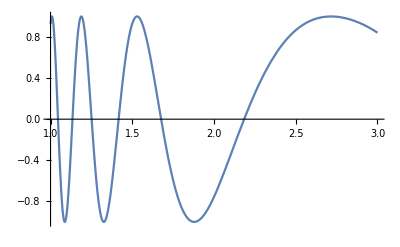

```mathematica
ClearAll["Global`*"]

kvRovnice = a*x^2+5x+2 == 0
kvJednoReseni = Solve[kvRovnice, x][[1]]

y[a_] = Sin[x^2] /. kvJednoReseni
Plot[y[a], {a, 1, 3}]
```

Příklad 4 (shodný s tím, co byl na cvičení)

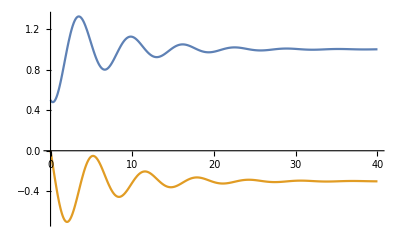

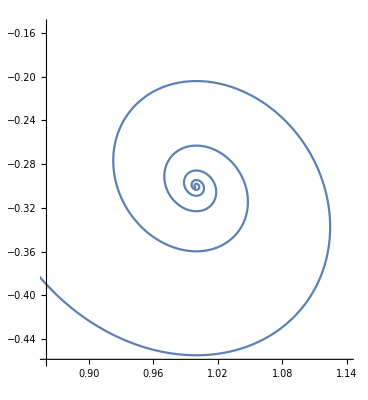

```mathematica
ClearAll["Global`*"]

reseniDiff = DSolve[{x1'[t]+x2[t]==-3/10*x1[t],x1[t]-x2'[t]==1, x1[0]==1/2,x2[0]==0}, {x1, x2}, {t, 0, 40}][[1]];

reseniX1 = reseniDiff[[1]];
reseniX2 = reseniDiff[[2]];

rovniceX1= x1 /. reseniX1;
rovniceX2 = x2 /. reseniX2;

Plot[{rovniceX1[t], rovniceX2[t]}, {t, 0, 40}]
ParametricPlot[{ rovniceX1[t], rovniceX2[t]}, {t, 0, 40}]
```

Příklad 5

```mathematica
ClearAll["Global`*"]

urok=0.1;
dni=30;

cistyUrok[castka_]:=castka*urok/100/365;
orezanyUrok[castka_]:=Floor[cistyUrok[castka],0.01];

cistyDalsiDen[castka_] := castka * (1+ cistyUrok[castka])
orezanyDalsiDen[castka_]:=Floor[castka * (1 + orezanyUrok[castka]),0.01]

cistyCelkem[castka_] := Nest[cistyDalsiDen, castka,dni];
orezanyCelkem[castka_] := Nest[orezanyDalsiDen, castka, dni];

castka = 10000;

pripsanoCelkem = orezanyCelkem[castka] - castka
vydelanoBanka = cistyCelkem[castka] - orezanyCelkem[castka]
```

21705.2

14055.7